```mathematica
(* Function to generate Quasi-random numbers with Van Der Corput sequence *)
VanDerCorput[base_,len_]:=Table[
With[{digits=Reverse@IntegerDigits[n,base]},
Sum[2^(-ii)*digits[[ii]],{ii,Length[digits]}]
],{n,len}]
```

```mathematica
(* Data to interpolate *)
ndata=600;
xlimit=4;
ylimit=5;
dataX=((2*xlimit)*VanDerCorput[2,ndata])-xlimit;
dataY=Table[i,{i,-ylimit,ylimit,2*ylimit/(ndata-1)}];
dataU=RandomReal[{-1,1},{ndata}];
dataV=RandomReal[{-1,1},{ndata}];

(* Field where data comes *)
fu[x_,y_]=x;
fv[x_,y_]=-y;

(* Evaluation of the field on random data *)
For[i=1,i≤ndata,i++,
dataU[[i]]=fu[dataX[[i]],dataY[[i]]];
dataV[[i]]=fv[dataX[[i]],dataY[[i]]];
];

(* Final data *)
data={dataX,dataY,dataU,dataV};
```

0.

0.

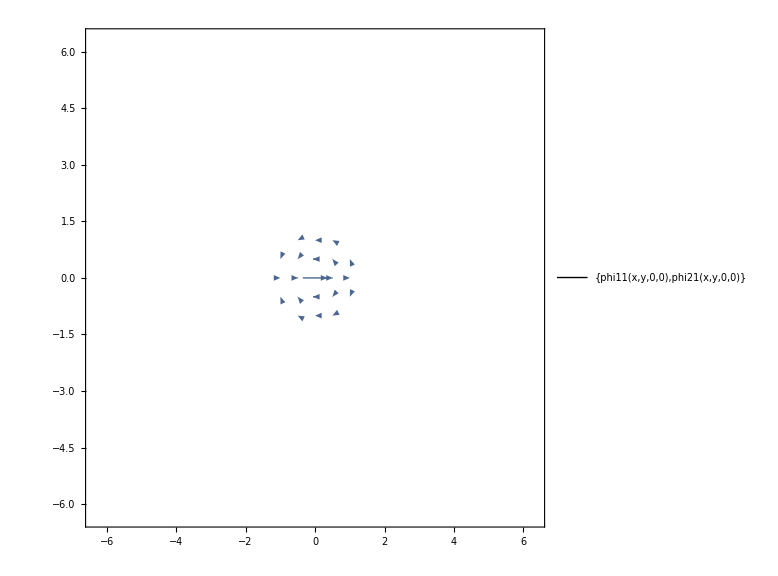

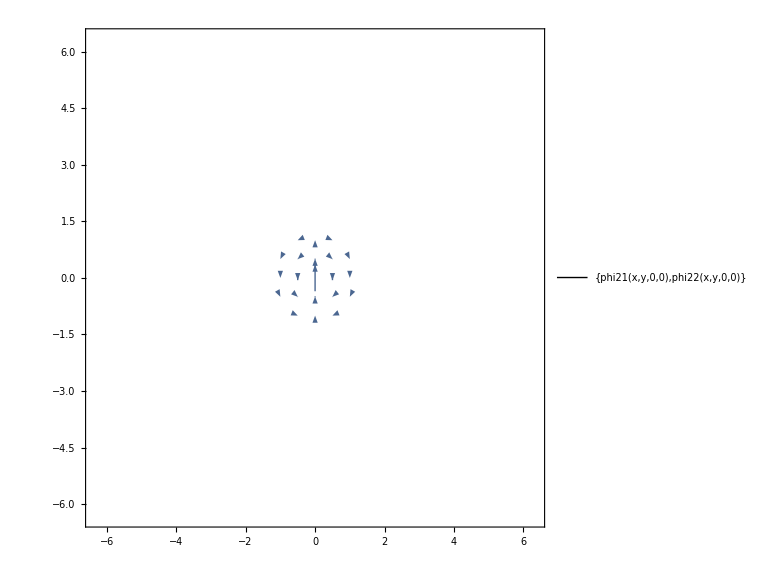

```mathematica
(* Defining functions *)
eps=3.8;
plus[x_]=Piecewise[{{x,x≥0},{0,x<0}}]; (* Needed to define Wendland functions *)

(* Defining RBF functions to occupy *)
f[x_,y_,x0_,y0_] =Exp[-eps^2 ((x-x0)^2+(y-y0)^2)];  (*Gaussian*)
g[x_,y_,x0_,y0_]=Sqrt[1+eps^2 ((x-x0)^2 + (y-y0)^2)];  (*Multiquadric*) 
h[x_,y_,x0_,y0_]=1/Sqrt[1+eps^2 ((x-x0)^2 + (y-y0)^2)]; (*Inverse Multiquadric*)
wendland0[x_,y_,x0_,y0_,s_]= plus[(1-EuclideanDistance[{x,y},{x0,y0}])]^(Floor[s/2]+1); (* Wendland's at k=0 *)

(* Actual basis function *)
psi[x_,y_,x0_,y0_] =f[x,y,x0,y0];

(* Coeficients of Phi matrix *)
phi11[x_,y_,x0_,y0_]=-D[psi[x,y,x0,y0],{y,2}];
phi12[x_,y_,x0_,y0_]=D[psi[x,y,x0,y0],{y,1},{x,1}];
phi21[x_,y_,x0_,y0_]=D[psi[x,y,x0,y0],{x,1},{y,1}];
phi22[x_,y_,x0_,y0_]=-D[psi[x,y,x0,y0],{x,2}];

(* Test to prove (phi11,phi21) and (phi12,phi22) are divergence free fields *)
Div[{phi11[x,y,x0,y0],phi21[x,y,x0,y0]},{x,y}]
Div[{phi12[x,y,x0,y0],phi22[x,y,x0,y0]},{x,y}]

VectorPlot[{phi11[x,y,0,0],phi21[x,y,0,0]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,VectorPoints->Fine]
VectorPlot[{phi21[x,y,0,0],phi22[x,y,0,0]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,VectorPoints->Fine]
```

```mathematica
(* Filling interpolation matrix A *)
A=RandomReal[{-1,1},{2ndata,2ndata}];

(* Sub matrix A11 *)
For[i=1,i ≤ndata,i++,
For[j=1, j≤ ndata, j++,
A[[i,j]]=Evaluate[phi11[data[[1,i]],data[[2,i]],data[[1,j]],data[[2,j]]]]
]
]
(* Sub matrix A12 *)
For[i=1,i ≤ndata,i++,
For[j=ndata+1, j≤ 2ndata, j++,
A[[i,j]]=Evaluate[phi12[data[[1,i]],data[[2,i]],data[[1,j-ndata]],data[[2,j-ndata]]]]
]
]
(*Sub matrix A21*)
For[i=ndata+1,i ≤2ndata,i++,
For[j=1, j≤ ndata, j++,
A[[i,j]]=Evaluate[phi21[data[[1,i-ndata]],data[[2,i-ndata]],data[[1,j]],data[[2,j]]]]
]
]
(* Sub matrix A22 *)
For[i=ndata+1,i ≤2ndata,i++,
For[j=ndata+1, j≤ 2ndata, j++,A[[i,j]]=Evaluate[phi22[data[[1,i-ndata]],data[[2,i-ndata]],data[[1,j-ndata]],data[[2,j-ndata]]]]
]
]
```

```mathematica
(* Determinant of interpolation matrix *)
Det[A]
```

1.80075342471086×10^977

```mathematica
(* Condition number of interpolation matrix *)
LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]
```

142.689

```mathematica
(* Plot of interpolation matrix *)
MatrixPlot[A,PlotTheme->"Detailed", ImageSize->Large]
```

-Graphics-

```mathematica
(* Vector with vector components at each point. *)
b=Join[data[[3]],data[[4]]];

(* Solve *)
c=LinearSolve[A,b];
```

```mathematica
(* Built final interpolating function *)
u=0;
v=0;
For[j=1,j≤ ndata,j++,
u = u+ c[[j]]*phi11[x,y,data[[1,j]],data[[2,j]]]+c[[j+ndata]]*phi12[x,y,data[[1,j]],data[[2,j]]];
v = v+ c[[j]]*phi21[x,y,data[[1,j]],data[[2,j]]]+c[[j+ndata]]*phi22[x,y,data[[1,j]],data[[2,j]]];
]
su[x_,y_] = u;
sv[x_,y_]=v;
```

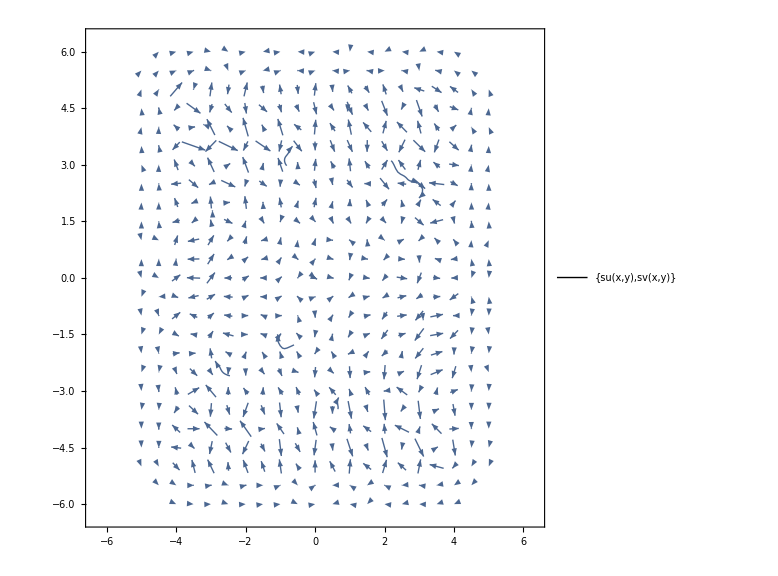

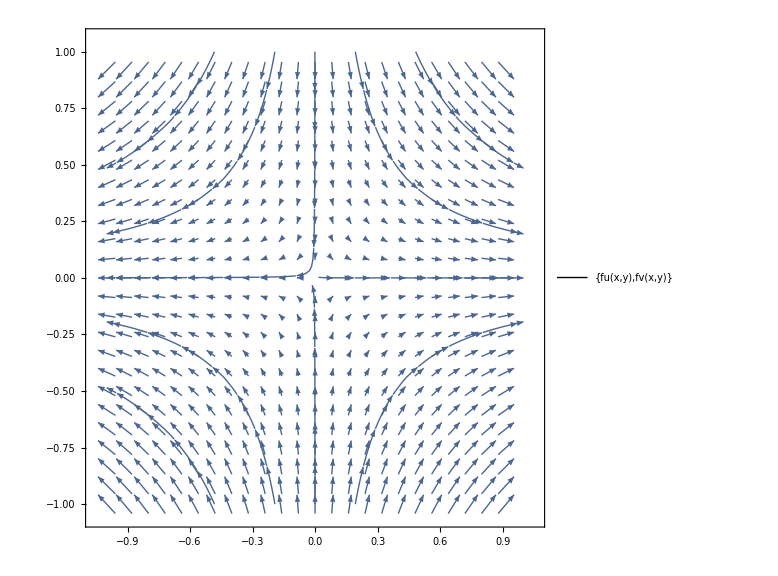

```mathematica
(* Plot of the resulting field and the original field *)
VectorPlot[{su[x,y],sv[x,y]},{x,-6,6},{y,-6,6},PlotTheme->"Detailed", ImageSize->Large,StreamPoints->10]
VectorPlot[{fu[x,y],fv[x,y]},{x,-1,1},{y,-1,1},PlotTheme->"Detailed", ImageSize->Large,StreamPoints->10]
```

```mathematica
(* Plot of the divergence in the resulting field *)
divs[x_,y_]=Div[{su[x,y],sv[x,y]},{x,y}];
Plot3D[divs[x,y],{x,-8,8},{y,-8,8},PlotRange->All,PlotTheme->"Detailed", ImageSize->Large]
```

-Graphics3D-